```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"velocity tools","init.nb"}]];
```

## Numeric Algorithm V1 (Via Primal Variables)

-Graphics-

```mathematica
proj[u_]:=Projection[u,{1,0}]
```

```mathematica
FindBisection[F0_,F1_,x0_,x1_,maxSteps_:1000]:=Module[{
y0Old=proj[x0],y1Old=proj[x1],
k=0,δ=Infinity,thr=$MachineEpsilon,results={},
yOld,z0,z1},
(* Return {solution, results} pair where results is a [k x 4] array with coulumns for {δ, y1Old, y0Old, yOld} after each step *)
While[Abs[δ]>thr&&k<maxSteps,
k+=1;
(* Step 1 *)
yOld=(y0Old+y1Old)/2;
(* Step 2 *)
z0=Subscript[𝒩̂, F0][(yOld-x0)/Subscript[γ, F0][yOld-x0]]/.λ->0.5;
z1=-Subscript[𝒩̂, F1][(x1-yOld)/Subscript[γ, F1][x1-yOld]]/.λ->0.5;
(* Step 3 *)
δ=proj[z0+z1][[1]];
(* Step 4 *)
If[Abs[δ]>thr,
If[proj[x0][[1]]<proj[x1][[1]],(* <- this if statement is new *)
If[δ>0,
y1Old=yOld;,
y0Old=yOld;
],
If[δ>0,
y0Old=yOld;,
y1Old=yOld;
]
]
];
AppendTo[results,{δ,y1Old,y0Old,yOld}]
];
{yOld,results}
]
```

### Transport From Point

```mathematica
defVel[F1,1.5{{0,1},{1,0},{0,-1},{-1,0}}]
defVel[F0,{{1,1},-{1,1},{1,-1},{-1,1}}]
```

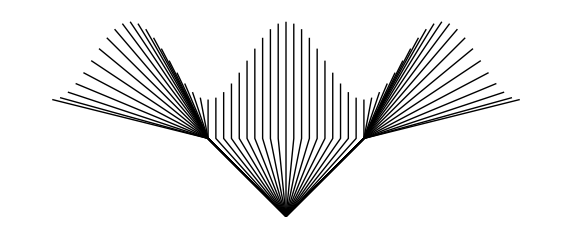

```mathematica
x0={0,-1.};

targets=Table[{p,1+0.5Cos[π p]},{p,-3,3,0.1}];

Show[Graphics@Table[
{y,r}=FindBisection[F0,F1,x0,targ];
Line[{x0,y,targ}],
{targ,targets}]]
```

### Derivation/Experiments

Warning: The code in this section was written while the algorithm was in development so certain segments will be inaccurate.

#### Numeric Algorithm V1 (Smooth)

```mathematica
First@Timing@Quiet@defVel[F0,1{Cos[t],Sin[t]}]
First@Timing@Quiet@defVel[F1,2{Cos[t],Sin[t]}]
```

0.001879

0.002335

```mathematica
x0={1,-1.};
x1={-1.,1};
y0Old=proj[x0];
y1Old=proj[x1];

δ=Infinity;
thr=$MachineEpsilon;
results={};
Monitor[
While[Abs[δ]>thr,
(* Step 1 *)
yOld=(y0Old+y1Old)/2;
(* Step 2 *)
z0=Subscript[𝒩̂, F0][(yOld-x0)/(Subscript[γ, F0][yOld-x0])];
z1=-Subscript[𝒩̂, F1][(x1-yOld)/(Subscript[γ, F1][x1-yOld])];
(* Step 3 *)
δ=proj[z0+z1][[1]];
(* Step 4 *)
If[δ!=0,
If[proj[x0][[1]]<proj[x1][[1]],
If[δ>0,
y1Old=yOld;,
y0Old=yOld;
],
If[δ>0,
y0Old=yOld;,
y1Old=yOld;
]
]
];
AppendTo[results,{δ,yOld}]
];
y0Old//N
,{δ,y0Old}//N]
```

{1.,0.}

```mathematica
GraphicsRow[{
ListLinePlot[results[[;;,1]],PlotRange->All,
PlotLabel->"Value of δ (Linear)"],
ListLinePlot[Abs[results[[;;,1]]],PlotRange->All,ScalingFunctions->"Log",
PlotLabel->"Value of |δ| (Log)"]
}]
```

-Graphics-

```mathematica
(* plot path during fist 10 steps of algorithm *)
ListAnimate@Table[Graphics[Line[{x0,xΣ,x1}],ImageSize->Small],{xΣ,results[[;;10,2]]}]
```

Part::take: Cannot take positions 1 through 10 in {{-0.333333+λ,{0.,0.}}}.

Table::iterb: Iterator {xΣ,{{-0.333333+λ,{0.,0.}}}⟦1;;10,2⟧} does not have appropriate bounds.

ListAnimate[Table[-Graphics-,{xΣ,{{-0.333333+λ,{0.,0.}}}⟦1;;10,2⟧}]]

#### Numeric Algorithm V1 (Polyhedral)

```mathematica
Clear[x,y]
defVel[F0,{{1,0},{0,1},{-1,0},{0,-1}}]
defVel[F1,{{1,1},{1,-1},{-1,1},{-1,-1}}]
GraphicsRow[LabeledPolarHullPlot/@{F0,F1}]
```

-Graphics-

Last::normal: Nonatomic expression expected at position 1 in Last[0].

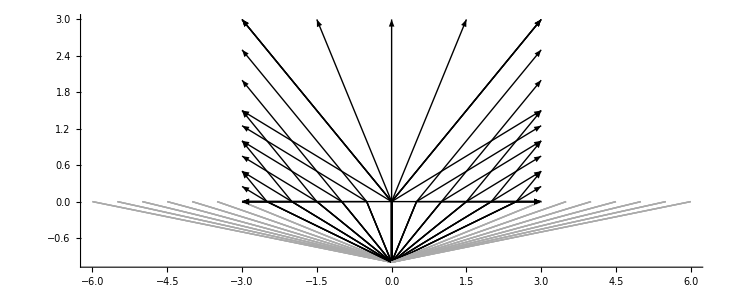

```mathematica
Show[Graphics[{
Arrowheads[Small],
Table[
Module[{x0={0,-1.},T=4,t=-.1,y0,v0,ζ0,ζ2s,v2s},
y0={t0,0};
t=Subscript[γ, F0][y0-x0];
v0=(y0-x0)/t;
(* Choose ζ0 ∈ Subscript[N, F0](v0) *)
ζ0=Subscript[𝒩̂, F0][v0](* points in normal cone properly scaled *);
(* calculate refracted angles with optimality conditions *)
ζ2s=Subscript[RefractedNormals, F1][ζ0];
v2s=Select[discretize/@(𝒩̂)_(F1^°)/@ζ2s,NonNegative@Last@#&];


If[T>Subscript[γ, F0][y0-x0],
{Black,Line[{x0,y0}],Tooltip[Arrow[{y0,(y0+(T-Subscript[γ, F0][y0-x0])#)}],{v0}]},
{Lighter@Gray,Line[{x0,y0}]}
]&/@v2s

],
{t0,-6,6,0.5}
]}],Axes->{True,False}]
```

```mathematica
Reverse[Show[{
Graphics[{Black,InfiniteLine[{0,0},{1,0}],Thick,Dashed,InfiniteLine[{0,0},{0,1}]}],
LabeledPolarPlot[F1,"(1)",TranslationTransform[#]@*ScalingTransform[{-1,-1}]],
Graphics[{Thick,Red,Arrow[{{0,0},#}]}]
},Axes->False,PlotRange->{1.5{-1,1},2{-0.5,1}},AspectRatio->{1,1},ImageSize->300]&/@Select[(F0^°)_pt,0<atan2[#]<π&]]
```

{-Graphics-,-Graphics-}

```mathematica
x0={0,-1};
x1={1,1};
y0Old=proj[x0];
y1Old=proj[x1];

k=0;
δ=Infinity;
thr=$MachineEpsilon;
results={};
Monitor[
While[Abs[δ]>thr&&k<100,
k+=1;
(* Step 1 *)
yOld=(y0Old+y1Old)/2;
(* Step 2 *)
z0=Subscript[𝒩̂, F0][(yOld-x0)/Subscript[γ, F0][yOld-x0]]/.λ->.5;
z1=-Subscript[𝒩̂, F1][(x1-yOld)/Subscript[γ, F1][x1-yOld]]/.λ->.5;
(* Step 3 *)
δ=proj[z0+z1][[1]];
(* Step 4 *)
If[Abs[δ]>thr,
If[proj[x0][[1]]<proj[x1][[1]],
If[δ>0,
y1Old=yOld;,
y0Old=yOld;
],
If[δ>0,
y0Old=yOld;,
y1Old=yOld;
]
]
];
AppendTo[results,{δ,y1Old,y0Old,yOld}]
];
,{δ,y0Old}//N]
{y1Old,y0Old,yOld}//N
```

{{7.88861×10^-31,0.},{0.,0.},{7.88861×10^-31,0.}}

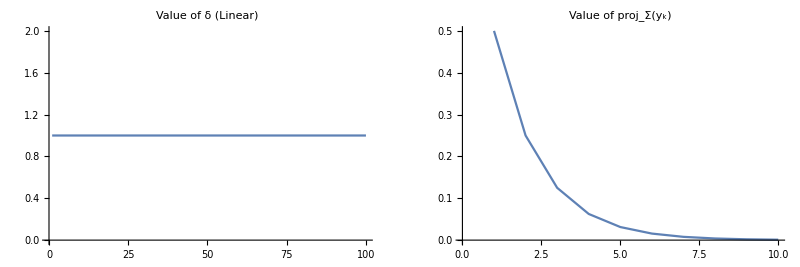

```mathematica
GraphicsRow[{
ListLinePlot[results[[;;,1]],PlotRange->All,
PlotLabel->"Value of δ (Linear)"],
ListLinePlot[results[[;;10,2,1]],PlotLabel->"Value of proj_Σ(y_k)"]
}]
```

```mathematica
TableForm[ArrayFlatten[{{List/@results[[;;,1]],results[[;;,2;;4,1]]}}],TableHeadings->{Range[1,Length[results]],{"δ","proj_Σ(y_1^Old)","proj_Σ(y_2^Old)","proj_Σ(y)"}}]
```

| δ | proj_Σ(y_1^Old) | proj_Σ(y_2^Old) | proj_Σ(y)
1 | 1 | 1/2 | 0 | 1/2
2 | 1 | 1/4 | 0 | 1/4
3 | 1 | 1/8 | 0 | 1/8
4 | 1 | 1/16 | 0 | 1/16
5 | 1 | 1/32 | 0 | 1/32
6 | 1 | 1/64 | 0 | 1/64
7 | 1 | 1/128 | 0 | 1/128
8 | 1 | 1/256 | 0 | 1/256
9 | 1 | 1/512 | 0 | 1/512
10 | 1 | 1/1024 | 0 | 1/1024
11 | 1 | 1/2048 | 0 | 1/2048
12 | 1 | 1/4096 | 0 | 1/4096
13 | 1 | 1/8192 | 0 | 1/8192
14 | 1 | 1/16384 | 0 | 1/16384
15 | 1 | 1/32768 | 0 | 1/32768
16 | 1 | 1/65536 | 0 | 1/65536
17 | 1 | 1/131072 | 0 | 1/131072
18 | 1 | 1/262144 | 0 | 1/262144
19 | 1 | 1/524288 | 0 | 1/524288
20 | 1 | 1/1048576 | 0 | 1/1048576
21 | 1 | 1/2097152 | 0 | 1/2097152
22 | 1 | 1/4194304 | 0 | 1/4194304
23 | 1 | 1/8388608 | 0 | 1/8388608
24 | 1 | 1/16777216 | 0 | 1/16777216
25 | 1 | 1/33554432 | 0 | 1/33554432
26 | 1 | 1/67108864 | 0 | 1/67108864
27 | 1 | 1/134217728 | 0 | 1/134217728
28 | 1 | 1/268435456 | 0 | 1/268435456
29 | 1 | 1/536870912 | 0 | 1/536870912
30 | 1 | 1/1073741824 | 0 | 1/1073741824
31 | 1 | 1/2147483648 | 0 | 1/2147483648
32 | 1 | 1/4294967296 | 0 | 1/4294967296
33 | 1 | 1/8589934592 | 0 | 1/8589934592
34 | 1 | 1/17179869184 | 0 | 1/17179869184
35 | 1 | 1/34359738368 | 0 | 1/34359738368
36 | 1 | 1/68719476736 | 0 | 1/68719476736
37 | 1 | 1/137438953472 | 0 | 1/137438953472
38 | 1 | 1/274877906944 | 0 | 1/274877906944
39 | 1 | 1/549755813888 | 0 | 1/549755813888
40 | 1 | 1/1099511627776 | 0 | 1/1099511627776
41 | 1 | 1/2199023255552 | 0 | 1/2199023255552
42 | 1 | 1/4398046511104 | 0 | 1/4398046511104
43 | 1 | 1/8796093022208 | 0 | 1/8796093022208
44 | 1 | 1/17592186044416 | 0 | 1/17592186044416
45 | 1 | 1/35184372088832 | 0 | 1/35184372088832
46 | 1 | 1/70368744177664 | 0 | 1/70368744177664
47 | 1 | 1/140737488355328 | 0 | 1/140737488355328
48 | 1 | 1/281474976710656 | 0 | 1/281474976710656
49 | 1 | 1/562949953421312 | 0 | 1/562949953421312
50 | 1 | 1/1125899906842624 | 0 | 1/1125899906842624
51 | 1 | 1/2251799813685248 | 0 | 1/2251799813685248
52 | 1 | 1/4503599627370496 | 0 | 1/4503599627370496
53 | 1 | 1/9007199254740992 | 0 | 1/9007199254740992
54 | 1 | 1/18014398509481984 | 0 | 1/18014398509481984
55 | 1 | 1/36028797018963968 | 0 | 1/36028797018963968
56 | 1 | 1/72057594037927936 | 0 | 1/72057594037927936
57 | 1 | 1/144115188075855872 | 0 | 1/144115188075855872
58 | 1 | 1/288230376151711744 | 0 | 1/288230376151711744
59 | 1 | 1/576460752303423488 | 0 | 1/576460752303423488
60 | 1 | 1/1152921504606846976 | 0 | 1/1152921504606846976
61 | 1 | 1/2305843009213693952 | 0 | 1/2305843009213693952
62 | 1 | 1/4611686018427387904 | 0 | 1/4611686018427387904
63 | 1 | 1/9223372036854775808 | 0 | 1/9223372036854775808
64 | 1 | 1/18446744073709551616 | 0 | 1/18446744073709551616
65 | 1 | 1/36893488147419103232 | 0 | 1/36893488147419103232
66 | 1 | 1/73786976294838206464 | 0 | 1/73786976294838206464
67 | 1 | 1/147573952589676412928 | 0 | 1/147573952589676412928
68 | 1 | 1/295147905179352825856 | 0 | 1/295147905179352825856
69 | 1 | 1/590295810358705651712 | 0 | 1/590295810358705651712
70 | 1 | 1/1180591620717411303424 | 0 | 1/1180591620717411303424
71 | 1 | 1/2361183241434822606848 | 0 | 1/2361183241434822606848
72 | 1 | 1/4722366482869645213696 | 0 | 1/4722366482869645213696
73 | 1 | 1/9444732965739290427392 | 0 | 1/9444732965739290427392
74 | 1 | 1/18889465931478580854784 | 0 | 1/18889465931478580854784
75 | 1 | 1/37778931862957161709568 | 0 | 1/37778931862957161709568
76 | 1 | 1/75557863725914323419136 | 0 | 1/75557863725914323419136
77 | 1 | 1/151115727451828646838272 | 0 | 1/151115727451828646838272
78 | 1 | 1/302231454903657293676544 | 0 | 1/302231454903657293676544
79 | 1 | 1/604462909807314587353088 | 0 | 1/604462909807314587353088
80 | 1 | 1/1208925819614629174706176 | 0 | 1/1208925819614629174706176
81 | 1 | 1/2417851639229258349412352 | 0 | 1/2417851639229258349412352
82 | 1 | 1/4835703278458516698824704 | 0 | 1/4835703278458516698824704
83 | 1 | 1/9671406556917033397649408 | 0 | 1/9671406556917033397649408
84 | 1 | 1/19342813113834066795298816 | 0 | 1/19342813113834066795298816
85 | 1 | 1/38685626227668133590597632 | 0 | 1/38685626227668133590597632
86 | 1 | 1/77371252455336267181195264 | 0 | 1/77371252455336267181195264
87 | 1 | 1/154742504910672534362390528 | 0 | 1/154742504910672534362390528
88 | 1 | 1/309485009821345068724781056 | 0 | 1/309485009821345068724781056
89 | 1 | 1/618970019642690137449562112 | 0 | 1/618970019642690137449562112
90 | 1 | 1/1237940039285380274899124224 | 0 | 1/1237940039285380274899124224
91 | 1 | 1/2475880078570760549798248448 | 0 | 1/2475880078570760549798248448
92 | 1 | 1/4951760157141521099596496896 | 0 | 1/4951760157141521099596496896
93 | 1 | 1/9903520314283042199192993792 | 0 | 1/9903520314283042199192993792
94 | 1 | 1/19807040628566084398385987584 | 0 | 1/19807040628566084398385987584
95 | 1 | 1/39614081257132168796771975168 | 0 | 1/39614081257132168796771975168
96 | 1 | 1/79228162514264337593543950336 | 0 | 1/79228162514264337593543950336
97 | 1 | 1/158456325028528675187087900672 | 0 | 1/158456325028528675187087900672
98 | 1 | 1/316912650057057350374175801344 | 0 | 1/316912650057057350374175801344
99 | 1 | 1/633825300114114700748351602688 | 0 | 1/633825300114114700748351602688
100 | 1 | 1/1267650600228229401496703205376 | 0 | 1/1267650600228229401496703205376

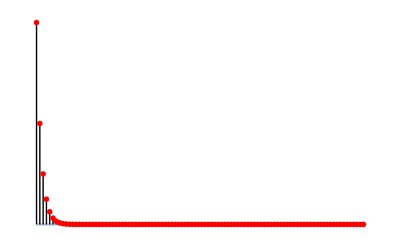

```mathematica
Show[{
Plot[0,{x,1,Length[results]},Axes->False,PlotStyle->Opacity[0.5]],
Graphics[{Line[{{#1,#2},{#1,#4}}],Red,PointSize[0.01],Point[{#1,#3}]}]&@@@ArrayFlatten[{{List/@Range[1,Length[results]],results[[;;,{2,4,3},1]]}}]
},PlotRange->All]
```

```mathematica
{y1Old,y0Old,yOld}//N
```

{{7.88861×10^-31,0.},{0.,0.},{7.88861×10^-31,0.}}

```mathematica
k
```

100

```mathematica
y0Old
```

{0,0}

```mathematica
δ
```

1

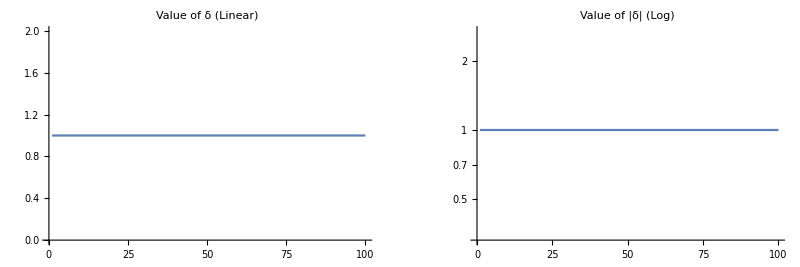

```mathematica
GraphicsRow[{
ListLinePlot[results[[;;,1]],PlotRange->All,
PlotLabel->"Value of δ (Linear)"],
ListLinePlot[Abs[results[[;;,1]]],PlotRange->All,ScalingFunctions->"Log",
PlotLabel->"Value of |δ| (Log)"]
}]
```

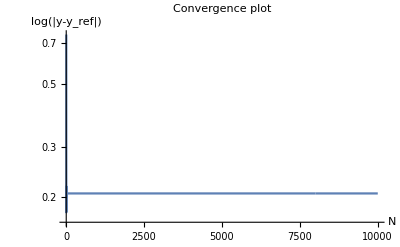

```mathematica
yy = results[[ ;;,2,1]];
refY =  0;
conv= Abs[yy - refY];
GraphicsRow[{
ListLinePlot[conv,PlotRange->All,ScalingFunctions->"Log",
PlotLabel->"Convergence plot", AxesLabel->{N,"log(|y-y_ref|)"}]
}]
```

```mathematica
(* plot path during fist 10 steps of algorithm *)
ListAnimate@Table[Graphics[Line[{x0,xΣ,x1}],ImageSize->Small],{xΣ,results[[;;10,2]]}]
```

```mathematica
First@Timing@Quiet@defVel[F0,{{-1,-1},{-1,1},{1,-1},{1,1},{2,0},{-1.5,0}}]
First@Timing@Quiet@defVel[F1,1.5{{0,1},{1,0},{0,-1},{-1,0}}]
(*First@Timing@Quiet@defVel[F0,{{1,1},-{1,1},{1,-1},{-1,1}}]*)
GraphicsRow[LabeledPolarHullPlot/@{F0,F1}]
```

0.007765

0.003996

-Graphics-

```mathematica
RandomReal[{0,1}]
```

0.0460231

```mathematica
x0={0,-2.};
x1={-6,1.};
y0Old=proj[x0];
y1Old=proj[x1];

k=0;
δ=Infinity;
thr=$MachineEpsilon;
results={};
Monitor[
While[Abs[δ]>thr&&k<100,
k+=1;
(* Step 1 *)
yOld=(y0Old+y1Old)/2;
(* Step 2 *)
z0=Subscript[𝒩̂, F0][(yOld-x0)/Subscript[γ, F0][yOld-x0]];
If[Not@FreeQ[z0,λ],Echo[{k,"z0",z0}];z0=z0/.λ->.5];
z1=-Subscript[𝒩̂, F1][(x1-yOld)/Subscript[γ, F1][x1-yOld]];
If[Not@FreeQ[z1,λ],Echo[{k,"z1",z1}];z1=z1/.λ->.5];
(* Step 3 *)
δ=proj[z0+z1][[1]];
(*Echo[{yOld,y0Old,y1Old,z0,z1,δ}];*)
(* Step 4 *)
If[Abs[δ]>thr,
If[δ>0,
y1Old=yOld;,
y0Old=yOld;
]
];
AppendTo[results,{δ,yOld}]
];
,{k,δ,y0Old}//N]
yOld
```

{-3.,0.}

```mathematica
z0
```

{-0.666667,0.333333}

```mathematica
z1
```

{0.666667,-0.666667}

```mathematica
Subscript[γ, F0][yOld-x0]+Subscript[γ, F1][x1-yOld]
```

5.33333

```mathematica
Subscript[γ, F0][{-6,0}-x0]+Subscript[γ, F1][x1-{-6,0}]
```

5.33333

```mathematica
δ
```

0.

Part::take: Cannot take positions 1 through 10 in {{0.,{-3.,0.}}}.

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: {{0.,{-3.,0.}}}⟦1;;10,2,1⟧ is not a list of numbers or pairs of numbers.

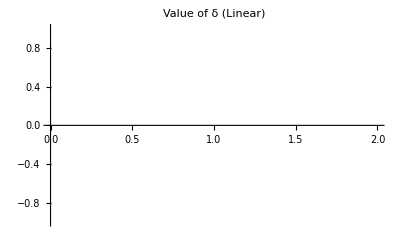

```mathematica
GraphicsRow[{
ListLinePlot[results[[;;,1]],PlotRange->All,
PlotLabel->"Value of δ (Linear)"],
ListLinePlot[results[[;;10,2,1]],PlotLabel->"Value of proj_Σ(y_k)"]
}]
```

```mathematica
(* plot path during fist 10 steps of algorithm *)
ListAnimate@Table[Graphics[Line[{x0,xΣ,x1}],ImageSize->Small],{xΣ,results[[;;10,2]]}]
```

Part::take: Cannot take positions 1 through 10 in {{0.,{-3.,0.}}}.

Table::iterb: Iterator {xΣ,{{0.,{-3.,0.}}}⟦1;;10,2⟧} does not have appropriate bounds.

ListAnimate[Table[-Graphics-,{xΣ,{{0.,{-3.,0.}}}⟦1;;10,2⟧}]]

## Numeric Algorithm V2 (Using Duality)

This algorithm is currently a work in progress.

-Graphics-

### Derivation

#### Numeric Algorithm V2 (Smooth)

```mathematica
First@Timing@Quiet@defVel[F0,1{Cos[t],Sin[t]}]
First@Timing@Quiet@defVel[F1,2{Cos[t],Sin[t]}]
```

0.029589

0.026892

```mathematica
x0={-1,-1}//N;
x1={1,1}//N;
y0Old=proj[x0];
y1Old=proj[x1];

k=0;
δ=Infinity;
thr=$MachineEpsilon;
results={};
Monitor[
While[Abs[δ]>thr&&k<=1*^4,
k+=1;
(* Step 1 *)
yOld=(y0Old+y1Old)/2;
(* Step 2 *)
z0=Subscript[𝒩̂, F0][(yOld-x0)/(Subscript[γ, F0][yOld-x0])];
z1=-Subscript[𝒩̂, F1][(x1-yOld)/(Subscript[γ, F1][x1-yOld])];
(* Step 3 *)
δ=proj[z0+z1][[1]];
(* Step 4 *)
If[δ!=0,
If[δ>0,
v1=(𝒩̂)_(F1^°)[z1];
y1Old=δ proj[v1];,
v0=(𝒩̂)_(F0^°)[z0];
y0Old=δ proj[v0];
]
];
AppendTo[results,{δ,yOld,y1Old,y0Old}]
];
y0Old//N
,{δ,yOld,y0Old,y1Old,k}//N]
```

{-0.0464664,0.}

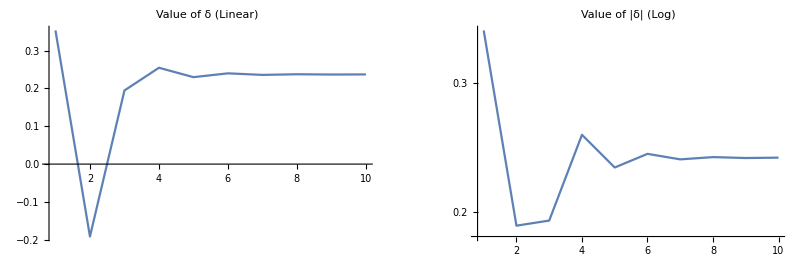

```mathematica
maxK=10;
GraphicsRow[{
ListLinePlot[results[[;;maxK,1]],PlotRange->All,
PlotLabel->"Value of δ (Linear)"],
ListLinePlot[Abs[results[[;;maxK,1]]],PlotRange->All,ScalingFunctions->"Log",
PlotLabel->"Value of |δ| (Log)"]
}]
```

## Exact Solution Derivation

```mathematica
First@Timing@Quiet@defVel[F0,{Cos[t],Sin [t]}]
First@Timing@Quiet@defVel[F1,2{Cos[t],Sin[t]}]

x0={-1,-1};
x1={1,1};
```

0.020103

0.020525

We can find the scaled normal cone of F1 from x0 at any point in space.

```mathematica
(𝒩̂)_(F1^°)[{x,y}-x0]
```

{(2 (1+x))/(√((1+x)^2+(1+y)^2)),(2 (1+y))/(√((1+x)^2+(1+y)^2))}

This plot shows the x-component of the dual vectors ζ_0 and ζ_1 along the interface Σ. The sum of these components is shown in green.

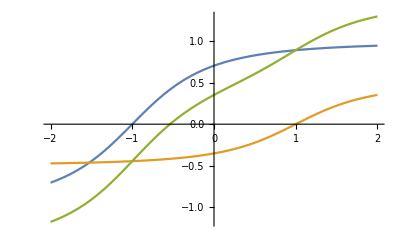

```mathematica
Plot[{
Subscript[𝒩̂, F0][{x,0}-x0][[1]],
-Subscript[𝒩̂, F1][x1-{x,0}][[1]],
Subscript[𝒩̂, F0][{x,0}-x0][[1]]-Subscript[𝒩̂, F1][x1-{x,0}][[1]]
},{x,-2,2}]
```

Where these curves are equal opposites is optimal crossing point, which can be solved exactly.

```mathematica
Subscript[𝒩̂, F0][{x,0}-x0][[1]]-Subscript[𝒩̂, F1][x1-{x,0}][[1]]
x/.Solve[%==0,x]
xOpt=First@Select[%,Im[#]==0&]
%//N
```

-(1-x)/(2 √(1+(1-x)^2))+(1+x)/(√(1+(1+x)^2))

{-1/6 √(6+(5967-216 √519)^(1/3)+3 (221+8 √519)^(1/3))+1/2 √(4/3-1/9 (5967-216 √519)^(1/3)-1/3 (221+8 √519)^(1/3)+20/(√(6+(5967-216 √519)^(1/3)+3 (221+8 √519)^(1/3))))}

-1/6 √(6+(5967-216 √519)^(1/3)+3 (221+8 √519)^(1/3))+1/2 √(4/3-1/9 (5967-216 √519)^(1/3)-1/3 (221+8 √519)^(1/3)+20/(√(6+(5967-216 √519)^(1/3)+3 (221+8 √519)^(1/3))))

-0.538264

What is the optimal travel time?

```mathematica
xΣ={xOpt,0};
t0=Subscript[γ, F0][xΣ-x0];
t1=Subscript[γ, F1][x1-xΣ];
T=t0+t1//N
```

2.01882

How does this fit in the previously computable solutions?

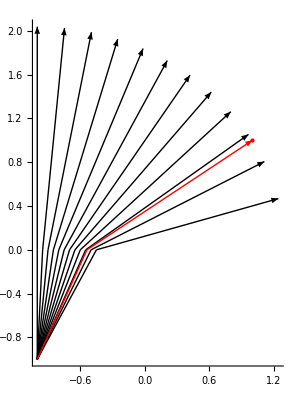

```mathematica
raytracePlt=Show[Graphics[{
Arrowheads[Small],
Table[
Module[{T=T,t,y0,v0,ζ0,ζ2s,v2s},
y0={t0,0};
t=Subscript[γ, F0][y0-x0];
v0=(y0-x0)/t;
(* Choose ζ0 ∈ Subscript[N, F0](v0) *)
ζ0=Subscript[𝒩̂, F0][v0](* properly scaled normal cone points *);
(* calculate refracted angles with optimality conditions *)
ζ2s=Subscript[RefractedNormals, F1][ζ0];
v2s=discretize/@Select[(𝒩̂)_(F1^°)/@ζ2s,NonNegative@Last@#&];


If[T>Subscript[γ, F0][y0-x0],
{Black,Line[{x0,y0}],Arrow[{y0,(y0+(T-Subscript[γ, F0][y0-x0])#)}]},
{Lighter@Gray,Line[{x0,y0}],Black,Arrow[{x0,x0+T v0}]}
]&/@v2s

],
{t0,-1,.5,0.05}
]},Axes->True]];
Show[raytracePlt,Graphics[{Red,Arrow[{x0,xΣ,x1}],Point[{1,1}]}]]
```